```mathematica
f[x_, r_, a_] = r x + a x^2 - x^3
Solve[f[x, r, a]==0, x]
```

{{x→0},{x→1/2 (a-√(a^2+4 r))},{x→1/2 (a+√(a^2+4 r))}}

```mathematica
Исходя из решений видим, что всегда существует особая точка в нуле(суперкритическая вилка намечается).
Остальные две точки являются действительными одновременно(при r>a^2/4), однако первая из них совпадает с нулем при r=0
```

{{x→0},{x→1/2 (a-√(a^2+4 r))},{x→1/2 (a+√(a^2+4 r))}}

{{x→0},{x→1/2 (-5-√(25+4 r))},{x→1/2 (-5+√(25+4 r))}}

{{x→0},{x→-√r},{x→√r}}

{{x→0},{x→1/2 (5-√(25+4 r))},{x→1/2 (5+√(25+4 r))}}

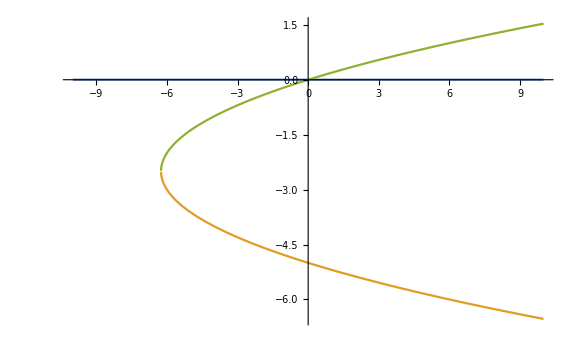

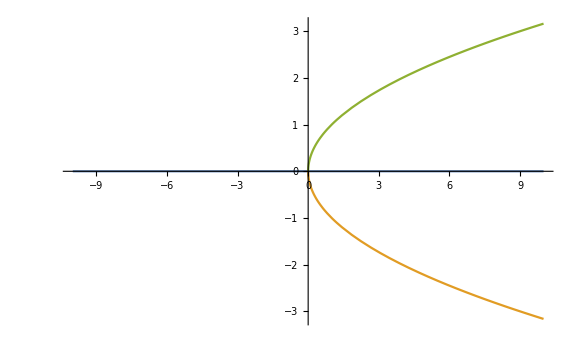

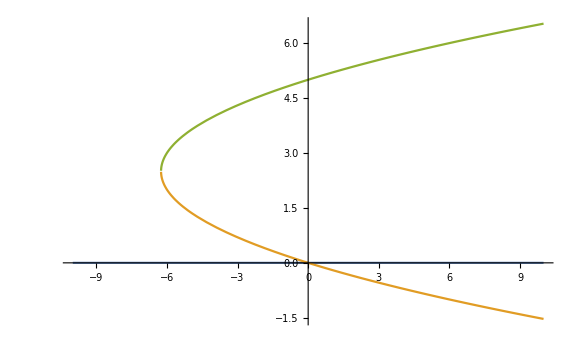

```mathematica
sol = Solve[f[x,r,a]==0,x]
solh1 = Solve[f[x,r,-5]==0,x]
solh2 = Solve[f[x,r,0]==0,x]
solh3 = Solve[f[x,r,5]==0,x]
Plot[{x /. solh1⟦1⟧, x /. solh1⟦2⟧, x /. solh1⟦3⟧},{r,-10,10}, ImageSize->Large, PlotRange->Full]
Plot[{x /. solh2⟦1⟧, x /. solh2⟦2⟧, x /. solh2⟦3⟧},{r,-10,10}, ImageSize->Large]
Plot[{x /. solh3⟦1⟧, x /. solh3⟦2⟧, x /. solh3⟦3⟧},{r,-10,10}, ImageSize->Large]
```

{{x→1/3 (a-√(a^2+3 r))},{x→1/3 (a+√(a^2+3 r))}}

{{r→0},{r→-a^2/4}}

{{r→0},{r→-a^2/4}}

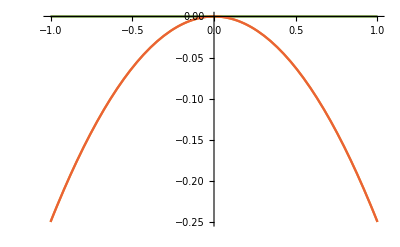

```mathematica
extrs = Solve[D[f[x,r,a], x]==0, x]
s1 = Solve[f[x/. extrs⟦1⟧, r, a] == 0, r]
s2 = Solve[f[x/. extrs⟦2⟧, r, a] == 0, r]
Plot[{r/. s1⟦1⟧, r/. s1⟦2⟧, r/. s2⟦1⟧, r/. s2⟦2⟧},{a,-1,1}]
```

```mathematica
Подставим точки в исходный график и проверим количество корней. Итого в верхней части графика 3 корня, внутри параболы 1 корень, 3 корня по сторонам параболы . На зеленой линии две(транскритическая). На красной линии 2 корня(вилка).
```